```mathematica
Needs["PlotLegends`"]
```

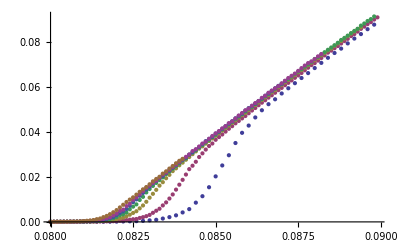

```mathematica
ListPlot[{gap5v9,gap10v9,gap20v9,gap30v9,gap40v9,gap50v9,gap100v9}]
```

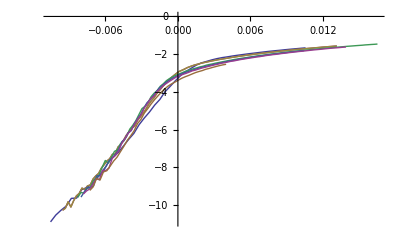

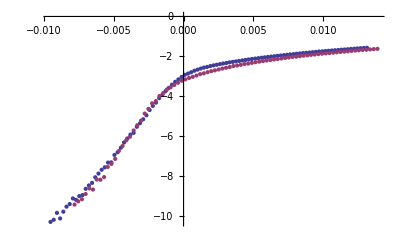

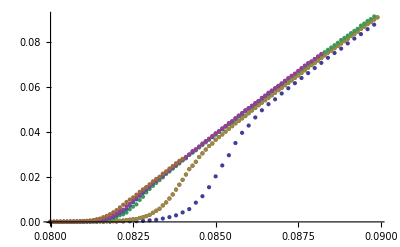

```mathematica
ClearAll[g];

v=9;

g[5][v]=gap5v9;
g[10][v]=gap10v9;
g[20][v]=gap20v9;
g[30][v]=gap30v9;
g[40][v]=gap40v9;
g[50][v]=gap50v9;
g[100][v]=gap100v9;


d0=0.081;
α=0.09;
b=10^-1.3;
β=-0.3;
z=0.09;

Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
,{l,{5,10,20,30,40,50,100}}]
ListLinePlot[{gs[5][9],gs[10][9],gs[10][9],gs[30][9],gs[40][9],gs[50][9],gs[100][9]}]
ListPlot[{gs[10][9],gs[50][9]}]
ListPlot[{g[5][9],g[10][9],g[10][9],g[30][9],g[40][9],g[50][9],g[100][9]}]
```

0.00267357  = val

0.08  = b

-0.38  = β

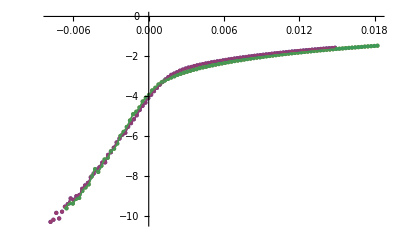

-Graphics-

```mathematica
ClearAll[gs,ig]
d0=0.081;
α=0.09;
z=0.09;
val=1000;


v=9;

g[5][v]=gap5v9;
g[10][v]=gap10v9;
g[20][v]=gap20v9;
g[30][v]=gap30v9;
g[40][v]=gap40v9;
g[50][v]=gap50v9;
g[100][v]=gap100v9;

l1=10;
l2=10;
l3=30;
l4=30;

For[b=0,b<0.2,b+=0.005,
For[β=-0.7,β<-0.1,β+=0.02,
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];
min=Max[gs[l1][v][[All,1]][[1]],gs[l2][v][[All,1]][[1]],gs[l3][v][[All,1]][[1]],gs[l4][v][[All,1]][[1]]];
max=Min[gs[l1][v][[All,1]][[Length[gs[l1][v]]]],gs[l2][v][[All,1]][[Length[gs[l2][v]]]],gs[l3][v][[All,1]][[Length[gs[l3][v]]]],gs[l4][v][[All,1]][[Length[gs[l4][v]]]]];
delta=(max-min)/50;
int=Sum[delta*(Max[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]-Min[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
bf=b;
βf=β;
minf=min;
maxf=max;
]
]
]

" = val"  val
" = b" bf
" = β" βf

Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-bf*(l*1000)^βf)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];

pic1=ListPlot[{gs[l1][v],gs[l2][v],gs[l3][v],gs[l4][v]}];
pic2=Plot[{ig[l1][v][x],ig[l2][v][x],ig[l3][v][x],ig[l4][v][x]},{x,minf,maxf}];
Show[{pic1,pic2}]
ListPlot[{g[5][9],g[10][9],g[10][9],g[30][9],g[40][9],g[50][9],g[100][9]}]
```

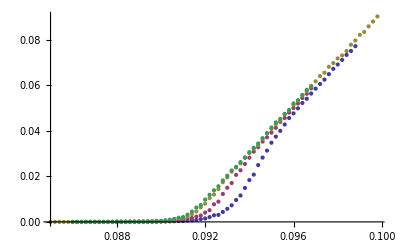

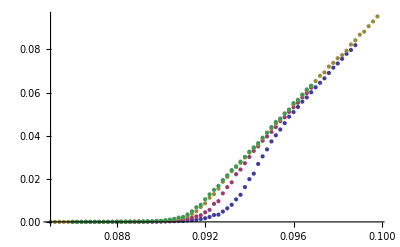

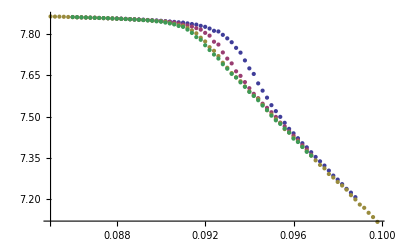

```mathematica
v="8";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v8=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v8=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v8=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];

gap10v8=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v8=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v8=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];

gap20v8=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v8=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v8=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];

gap30v8=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v8=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v8=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];


ListPlot[{gap5v8,gap10v8,gap20v8,gap30v8},PlotRange->Full]
ListPlot[{vel5v8,vel10v8,vel20v8,vel30v8},PlotRange->Full]
ListPlot[{avel5v8,avel10v8,avel20v8,avel30v8}]
```

0.00336169  = val

0.165  = b

-0.52  = β

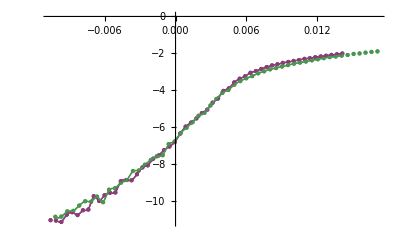

-Graphics-

```mathematica
ClearAll[gs,ig]
d0=0.08925417883112817;
α=0.09;
z=0.09;
val=1000;

v=8;

g[5][v]=gap5v8;
g[10][v]=gap10v8;
g[20][v]=gap20v8;
g[30][v]=gap30v8;


l1=10;
l2=10;
l3=30;
l4=30;

For[b=0,b<0.2,b+=0.005,
For[β=-0.7,β<-0.1,β+=0.02,
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];
min=Max[gs[l1][v][[All,1]][[1]],gs[l2][v][[All,1]][[1]],gs[l3][v][[All,1]][[1]],gs[l4][v][[All,1]][[1]]];
max=Min[gs[l1][v][[All,1]][[Length[gs[l1][v]]]],gs[l2][v][[All,1]][[Length[gs[l2][v]]]],gs[l3][v][[All,1]][[Length[gs[l3][v]]]],gs[l4][v][[All,1]][[Length[gs[l4][v]]]]];
delta=(max-min)/50;
int=Sum[delta*(Max[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]-Min[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
bf=b;
βf=β;
minf=min;
maxf=max;
]
]
]

" = val"  val
" = b" bf
" = β" βf

Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-bf*(l*1000)^βf)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];

pic1=ListPlot[{gs[l1][v],gs[l2][v],gs[l3][v],gs[l4][v]}];
pic2=Plot[{ig[l1][v][x],ig[l2][v][x],ig[l3][v][x],ig[l4][v][x]},{x,minf,maxf}];
Show[{pic1,pic2}]
ListPlot[{g[5][v],g[10][v],g[20][v],g[30][v]}]
```

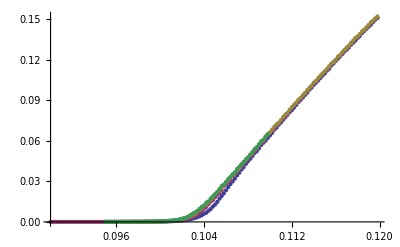

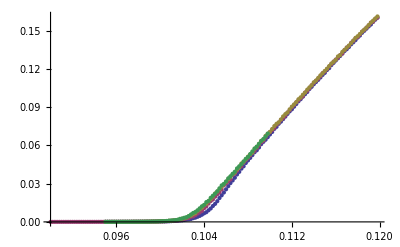

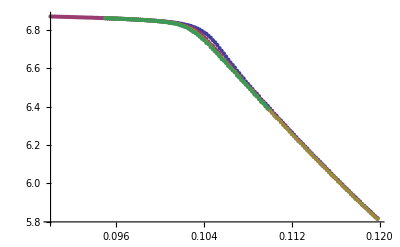

```mathematica
v="7";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v8=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v8=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v8=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];

gap10v8=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v8=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v8=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];

gap20v8=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v8=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v8=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];

gap30v8=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v8=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v8=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];


ListPlot[{gap5v8,gap10v8,gap20v8,gap30v8},PlotRange->Full]
ListPlot[{vel5v8,vel10v8,vel20v8,vel30v8},PlotRange->Full]
ListPlot[{avel5v8,avel10v8,avel20v8,avel30v8}]
```

```mathematica
***
```

0.00688785  = val

0.185  = b

-0.54  = β

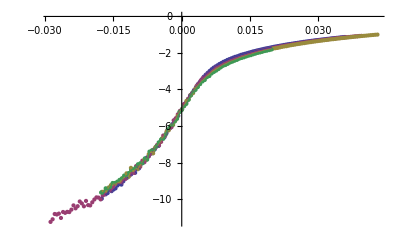

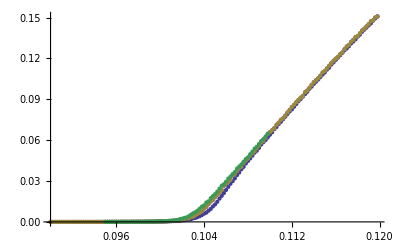

```mathematica
ClearAll[gs,ig]
d0=0.10129517685639909;
α=0.09;
z=0.09;
val=1000;

v=7;

g[5][v]=gap5v8;
g[10][v]=gap10v8;
g[20][v]=gap20v8;
g[30][v]=gap30v8;


l1=5;
l2=10;
l3=20;
l4=30;

For[b=0,b<0.2,b+=0.005,
For[β=-0.7,β<-0.1,β+=0.02,
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];
min=Max[gs[l1][v][[All,1]][[1]],gs[l2][v][[All,1]][[1]],gs[l3][v][[All,1]][[1]],gs[l4][v][[All,1]][[1]]];
max=Min[gs[l1][v][[All,1]][[Length[gs[l1][v]]]],gs[l2][v][[All,1]][[Length[gs[l2][v]]]],gs[l3][v][[All,1]][[Length[gs[l3][v]]]],gs[l4][v][[All,1]][[Length[gs[l4][v]]]]];
delta=(max-min)/50;
int=Sum[delta*(Max[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]-Min[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
bf=b;
βf=β;
minf=min;
maxf=max;
]
]
]

" = val"  val
" = b" bf
" = β" βf

Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-bf*(l*1000)^βf)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];

pic1=ListPlot[{gs[l1][v],gs[l2][v],gs[l3][v],gs[l4][v]}];
pic2=Plot[{ig[l1][v][x],ig[l2][v][x],ig[l3][v][x],ig[l4][v][x]},{x,minf,maxf}];
Show[{pic1,pic2}]
ListPlot[{g[5][v],g[10][v],g[10][v],g[30][v]}]
```

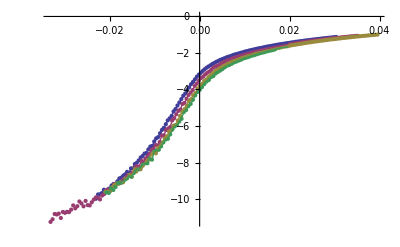

-Graphics-

```mathematica
bf=0.2407530406366698;
βf=-0.47;
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-bf*(l*1000)^βf)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];

pic1=ListPlot[{gs[l1][v],gs[l2][v],gs[l3][v],gs[l4][v]}];
pic2=Plot[{ig[l1][v][x],ig[l2][v][x],ig[l3][v][x],ig[l4][v][x]},{x,minf,maxf}];
Show[{pic1,pic2}]
ListPlot[{g[5][v],g[10][v],g[10][v],g[30][v]}]
```

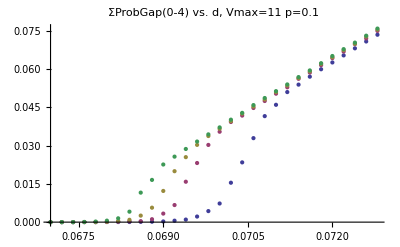

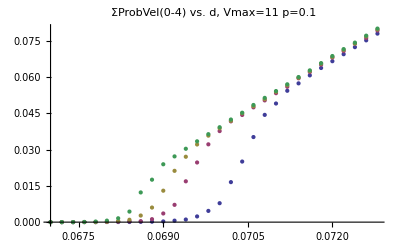

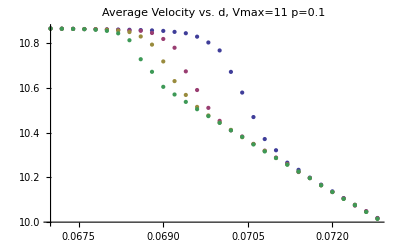

```mathematica
v="11";
p="0.1";
g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l50k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

ngap="4";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v11=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v11=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v5k1]}];
avel5v11=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v11=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v11=Table[{v10k1[[All,1]][[j]],(1-Sum[v10k1[[All,i]][[j]],{i,3,13}])+Sum[v10k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v10k1]}];
avel10v11=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v11=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v11=Table[{v20k1[[All,1]][[j]],(1-Sum[v20k1[[All,i]][[j]],{i,3,13}])+Sum[v20k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v20k1]}];
avel20v11=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
gap30v11=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v11=Table[{v30k1[[All,1]][[j]],(1-Sum[v30k1[[All,i]][[j]],{i,3,13}])+Sum[v30k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v30k1]}];
avel30v11=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];
gap50v11=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g50k1]}];
vel50v11=Table[{v50k1[[All,1]][[j]],(1-Sum[v50k1[[All,i]][[j]],{i,3,13}])+Sum[v50k1[[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[v50k1]}];
avel50v11=Table[{av50k1[[All,1]][[j]],av50k1[[All,2]][[j]]},{j,1,Length[av50k1]}];


ListPlot[{gap10v11,gap20v11,gap30v11,gap50v11},PlotLabel->"ΣProbGap(0-"<>ngap<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{vel10v11,vel20v11,vel30v11,vel50v11},PlotLabel->"ΣProbVel(0-"<>nvel<>") vs. d, Vmax="<>v<>"  p="<>p,PlotLegend->{"10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{avel10v11,avel20v11,avel30v11,avel50v11},PlotLabel->"Average Velocity vs. d, Vmax="<>v<>"  p="<>p,PlotRange->Full,PlotLegend->{"10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

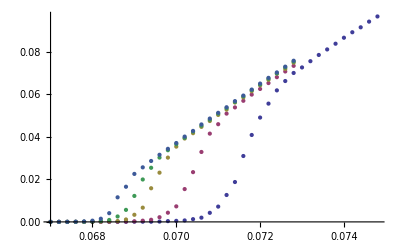

```mathematica
ListPlot[{gap5v11,gap10v11,gap20v11,gap30v11,gap50v11}]
```

0.009684  = val

0.185  = b

-0.5  = β

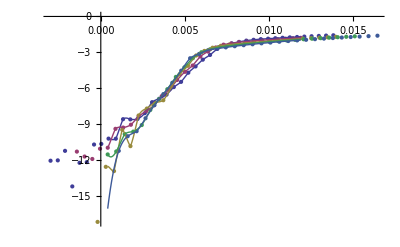

-Graphics-

```mathematica
ClearAll[gs,ig]
d0=0.06576996509783684;
α=0.09;
z=0.09;
val=1000;

v=11;

g[5][v]=gap5v11;
g[10][v]=gap10v11;
g[20][v]=gap20v11;
g[30][v]=gap30v11;
g[50][v]=gap50v11;


l1=5;
l2=10;
l3=20;
l4=30;

For[b=0,b<0.2,b+=0.005,
For[β=-0.7,β<-0.1,β+=0.02,
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4,l5}}
];
min=Max[gs[l1][v][[All,1]][[1]],gs[l2][v][[All,1]][[1]],gs[l3][v][[All,1]][[1]],gs[l4][v][[All,1]][[1]]];
max=Min[gs[l1][v][[All,1]][[Length[gs[l1][v]]]],gs[l2][v][[All,1]][[Length[gs[l2][v]]]],gs[l3][v][[All,1]][[Length[gs[l3][v]]]],gs[l4][v][[All,1]][[Length[gs[l4][v]]]]];
delta=(max-min)/50;
int=Sum[delta*(Max[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta],ig[l5][v][min+k*delta]]-Min[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta],ig[l5][v][min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
bf=b;
βf=β;
minf=min;
maxf=max;
]
]
]

" = val"  val
" = b" bf
" = β" βf

l5=50;
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-bf*(l*1000)^βf)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4,l5}}
];

pic1=ListPlot[{gs[l1][v],gs[l2][v],gs[l3][v],gs[l4][v],gs[l5][v]}];
pic2=Plot[{ig[l1][v][x],ig[l2][v][x],ig[l3][v][x],ig[l4][v][x],ig[l5][v][x]},{x,minf,maxf}];
Show[{pic1,pic2}]
ListPlot[{g[5][v],g[10][v],g[20][v],g[30][v],g[50][v]}]
```

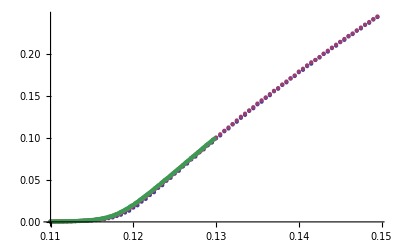

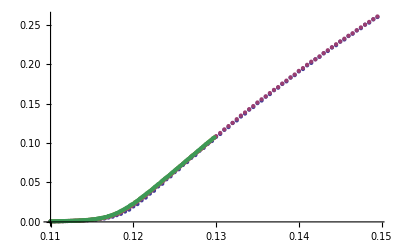

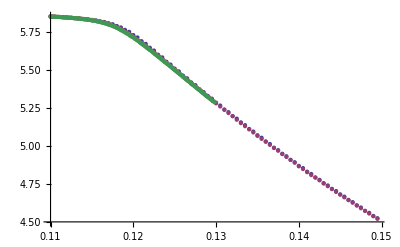

```mathematica
v="6";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

ngap="3";
nvel="3";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v8=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v8=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v8=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];

gap10v8=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v8=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v8=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];

gap20v8=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v8=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v8=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];

gap30v8=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v8=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v8=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];


ListPlot[{gap5v8,gap10v8,gap20v8,gap30v8},PlotRange->Full]
ListPlot[{vel5v8,vel10v8,vel20v8,vel30v8},PlotRange->Full]
ListPlot[{avel5v8,avel10v8,avel20v8,avel30v8}]
```

0.00644783  = val

0.195  = b

-0.56  = β

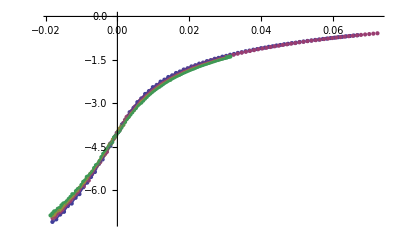

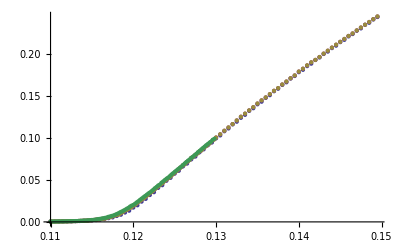

```mathematica
ClearAll[gs,ig]
d0=0.11675839124676939;
α=0.09;
z=0.09;
val=1000;

v=6;

g[5][v]=gap5v8;
g[10][v]=gap10v8;
g[20][v]=gap20v8;
g[30][v]=gap30v8;


l1=5;
l2=10;
l3=20;
l4=30;

For[b=0,b<0.2,b+=0.005,
For[β=-0.7,β<-0.1,β+=0.02,
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];
min=Max[gs[l1][v][[All,1]][[1]],gs[l2][v][[All,1]][[1]],gs[l3][v][[All,1]][[1]],gs[l4][v][[All,1]][[1]]];
max=Min[gs[l1][v][[All,1]][[Length[gs[l1][v]]]],gs[l2][v][[All,1]][[Length[gs[l2][v]]]],gs[l3][v][[All,1]][[Length[gs[l3][v]]]],gs[l4][v][[All,1]][[Length[gs[l4][v]]]]];
delta=(max-min)/50;
int=Sum[delta*(Max[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]-Min[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
bf=b;
βf=β;
minf=min;
maxf=max;
]
]
]

" = val"  val
" = b" bf
" = β" βf

Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-bf*(l*1000)^βf)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];

pic1=ListPlot[{gs[l1][v],gs[l2][v],gs[l3][v],gs[l4][v]}];
pic2=Plot[{ig[l1][v][x],ig[l2][v][x],ig[l3][v][x],ig[l4][v][x]},{x,minf,maxf}];
Show[{pic1,pic2}]
ListPlot[{g[5][v],g[10][v],g[10][v],g[30][v]}]
```

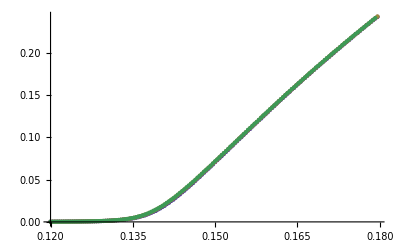

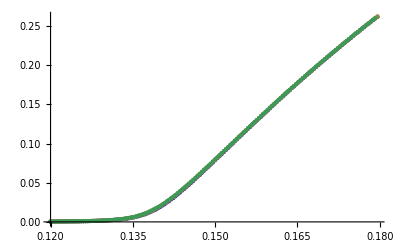

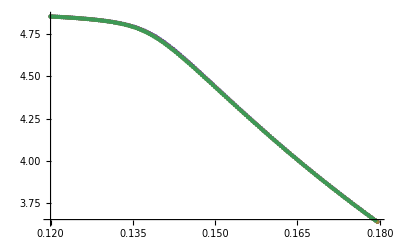

```mathematica
v="5";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l10k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l20k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l30k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];

ngap="2";
nvel="2";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;

gap5v8=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v8=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v8=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];

gap10v8=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v8=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v8=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];

gap20v8=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v8=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v8=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];

gap30v8=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g30k1]}];
vel30v8=Table[{v30k1[[All,1]][[j]],Sum[v30k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v30k1]}];
avel30v8=Table[{av30k1[[All,1]][[j]],av30k1[[All,2]][[j]]},{j,1,Length[av30k1]}];


ListPlot[{gap5v8,gap10v8,gap20v8,gap30v8},PlotRange->Full]
ListPlot[{vel5v8,vel10v8,vel20v8,vel30v8},PlotRange->Full]
ListPlot[{avel5v8,avel10v8,avel20v8,avel30v8}]
```

0.0161713  = val

0.05  = b

-0.26  = β

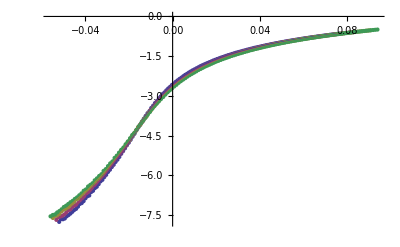

```mathematica
ClearAll[gs,ig]
d0=0.13868040135702742;
α=0.09;
z=0.09;
val=1000;

v=5;

g[5][v]=gap5v8;
g[10][v]=gap10v8;
g[20][v]=gap20v8;
g[30][v]=gap30v8;


l1=5;
l2=10;
l3=20;
l4=30;

For[b=0,b<0.2,b+=0.005,
For[β=-0.7,β<-0.1,β+=0.02,
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];
min=Max[gs[l1][v][[All,1]][[1]],gs[l2][v][[All,1]][[1]],gs[l3][v][[All,1]][[1]],gs[l4][v][[All,1]][[1]]];
max=Min[gs[l1][v][[All,1]][[Length[gs[l1][v]]]],gs[l2][v][[All,1]][[Length[gs[l2][v]]]],gs[l3][v][[All,1]][[Length[gs[l3][v]]]],gs[l4][v][[All,1]][[Length[gs[l4][v]]]]];
delta=(max-min)/50;
int=Sum[delta*(Max[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]-Min[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
bf=b;
βf=β;
minf=min;
maxf=max;
]
]
]

" = val"  val
" = b" bf
" = β" βf

Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0-bf*(l*1000)^βf)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];

pic1=ListPlot[{gs[l1][v],gs[l2][v],gs[l3][v],gs[l4][v]}];
pic2=Plot[{ig[l1][v][x],ig[l2][v][x],ig[l3][v][x],ig[l4][v][x]},{x,minf,maxf}];
Show[{pic1,pic2}]
ListPlot[{g[5][v],g[10][v],g[10][v],g[30][v]}]
```